```mathematica
Kimura[x_,y_,t_,n_]:= Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
```

```mathematica
compare[params_,pathIntegrals_,scenario_,dStep_]:=
Module[{solution,haywardScenario,pstart,ptime,statDist,p=Association[params]},
ptime=p[time];
pstart=p[start];
Print["Running NDSolve for Scenario ",scenario];
solution=NDSolve[{
D[f[y,t],t]==
 -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] +1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==
Evaluate[
PDF[TriangularDistribution[{(pstart - 0.001),(pstart + 0.001)},pstart],y]]
} /. params,f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];

Print["Computing Hayward Solution for Scenario ",scenario];
haywardScenario= Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pathIntegrals[[j]][[scenario]],{j,1,5}]);

Print[Plot[{
Evaluate[haywardScenario/.params/. {t->ptime,x->pstart}],
Evaluate[f[y,t] /.solution /. {t->ptime}]
},{y, 0,1},
PlotLabel->StringForm["Scenario ``, α=``,VG=``",scenario,p[α],p[VG]],
PlotLegends->{"Path Integral","Numerical Solution"}
]];

Print["Computing Statistical Distance for Scenario ",scenario];
statDist = 1/2 NIntegrate[Abs[
Evaluate[haywardScenario/.params/.{x->pstart,t -> ptime}] - Evaluate[{f[y, ptime]} /. solution]],
{y,0,1}];
Print["Statistical Distance",statDist];
haywardScenario/.params/.{x->pstart,t -> ptime}/.{y->Table[i,{i,0,1,dStep}]}
]
```

```mathematica
prettyTime[s_]:=
UnitConvert[Quantity[s,"Seconds"],MixedUnit[{"Hours","Minutes","Seconds"}]]
runComparisonAndSave[scenarios_,inFile_,outFile_,dStep_]:=
Block[{result,pints},
Get[FileNameJoin[{NotebookDirectory[],inFile}]];
result=AbsoluteTiming[Transpose[Flatten/@Transpose[
Table[{
Table[i,{j,0,1,.001}],
Table[j,{j,0,1,.001}],
compare[scenarios[[i]],pints,i,dStep]
},{i,1,Length[scenarios]}]]]];
Export[FileNameJoin[{NotebookDirectory[],outFile}],result[[2]],
"CSV",TableHeadings->{"scenario","end_freq","density"}];
Print[StringForm["Ran comparison in ``",prettyTime[result[[1]]]]];
]
```

```mathematica
baseParams={
start->0.1,
time->0.05,
Λ->1, 
Ne -> 500,
W->1
};
```

{{start→0.1,time→0.05,Λ→1,Ne→500,W→1,α→0.005,VG→0.00224995},{start→0.1,time→0.05,Λ→1,Ne→500,W→1,α→0.01,VG→0.00705098},{start→0.1,time→0.05,Λ→1,Ne→500,W→1,α→0.005,VG→0.019861},{start→0.1,time→0.05,Λ→1,Ne→500,W→1,α→0.01,VG→0.0568599}}

Running NDSolve for Scenario 1

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

Computing Hayward Solution for Scenario 1

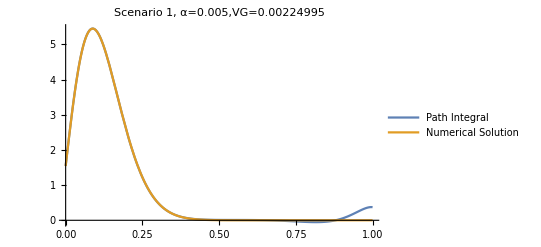

Computing Statistical Distance for Scenario 1

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.880844}. NIntegrate obtained 0.0325838 and 5.20766×10^-8 for the integral and error estimates.

Statistical Distance{{0.0162919}}

Running NDSolve for Scenario 2

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

Computing Hayward Solution for Scenario 2

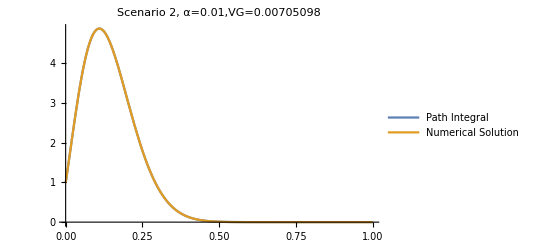

Computing Statistical Distance for Scenario 2

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0683438}. NIntegrate obtained 0.0000217752 and 4.52336×10^-11 for the integral and error estimates.

Statistical Distance{{0.0000108876}}

Running NDSolve for Scenario 3

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve::bcart will be suppressed during this calculation.

Computing Hayward Solution for Scenario 3

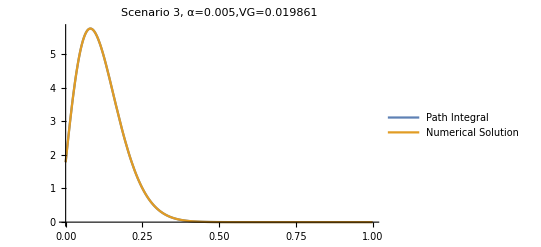

Computing Statistical Distance for Scenario 3

Statistical Distance{{9.98597×10^-6}}

Running NDSolve for Scenario 4

Computing Hayward Solution for Scenario 4

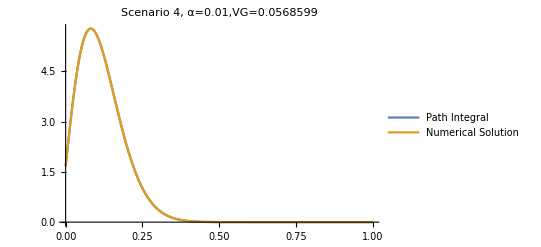

Computing Statistical Distance for Scenario 4

Statistical Distance{{0.000483078}}

Ran comparison in 0

```mathematica
scenarios=Join[baseParams,#]&/@{
{α->0.005,VG->0.002249954},
{α->0.01,VG->0.007050979},
{α->0.005,VG->0.019860999},
{α->0.01,VG->0.056859878}
}

runComparisonAndSave[
scenarios,
"integrals/out/path-integrals-simulations.m",
"integrals/out/linked_sim_densities.csv",
.001
]
```

```mathematica
Clear[pints,result]
```

{{start→0.1,time→0.05,Λ→1,Ne→500,W→1,α→0.005,VG→0.00231845},{start→0.1,time→0.05,Λ→1,Ne→500,W→1,α→0.01,VG→0.00742792},{start→0.1,time→0.05,Λ→1,Ne→500,W→1,α→0.005,VG→0.0229107},{start→0.1,time→0.05,Λ→1,Ne→500,W→1,α→0.01,VG→0.0743196}}

Running NDSolve for Scenario 1

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

Computing Hayward Solution for Scenario 1

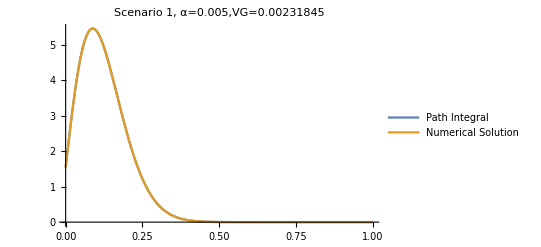

Computing Statistical Distance for Scenario 1

Statistical Distance{{9.85936×10^-6}}

Running NDSolve for Scenario 2

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

Computing Hayward Solution for Scenario 2

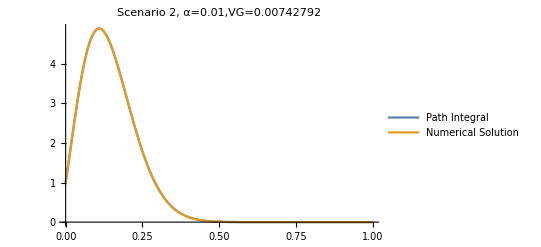

Computing Statistical Distance for Scenario 2

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.240219}. NIntegrate obtained 0.0000217798 and 2.64956×10^-11 for the integral and error estimates.

Statistical Distance{{0.0000108899}}

Running NDSolve for Scenario 3

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve::bcart will be suppressed during this calculation.

Computing Hayward Solution for Scenario 3

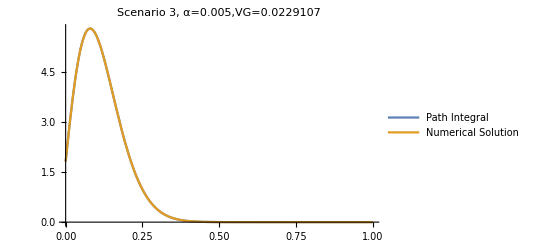

Computing Statistical Distance for Scenario 3

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.179672}. NIntegrate obtained 0.0000203719 and 3.20098×10^-11 for the integral and error estimates.

Statistical Distance{{0.0000101859}}

Running NDSolve for Scenario 4

Computing Hayward Solution for Scenario 4

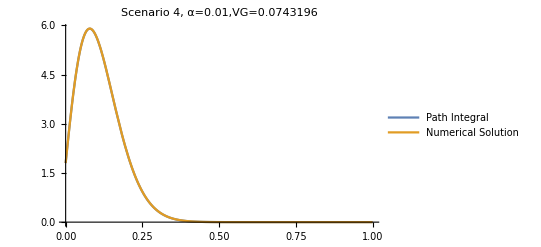

Computing Statistical Distance for Scenario 4

Statistical Distance{{0.000507426}}

Ran comparison in 0

```mathematica
scenarios=Join[baseParams,#]&/@{
{α->0.005,VG->0.00231845390822375},
{α->0.01,VG->0.00742792066842},
{α->0.005,VG->0.0229107227362775},
{α->0.01,VG->0.07431959268402}
}

runComparisonAndSave[
scenarios,
"integrals/out/path-integrals-simulations-unlinked.m",
"integrals/out/unlinked_sim_densities.csv",
.001
]
```

```mathematica
Clear[pints,result]
```